```mathematica
Lorentzian[x_,x0_,γ_]:=1/(Pi*γ(1+((x-x0)/γ)^2))
```

```mathematica
1/(Pi*γ(1+((x-x0)/γ)^2))
```

1/(π (1+(x-x0)^2/γ^2) γ)

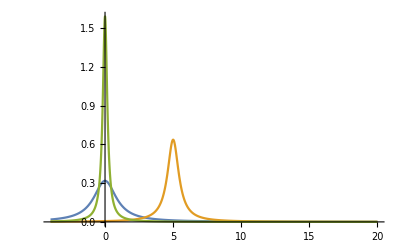

```mathematica
Plot[{Lorentzian[x,0,1],Lorentzian[x,5,.5],Lorentzian[x,0,.2]},{x,-4,20},PlotRange->Full]
```



```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
Plot3D[Lorentzian[x,Sin[x0],.8],{x0,0,2Pi},{x,-4,4},PlotRange->Full,AxesLabel->{"x0","x","L(γ,x0,x)"},ViewPoint->{0, 0, 2}]
```

-Graphics3D-

```mathematica
Table[Sum[Lorentzian[x,0,.8],{i,1,n}],{n,50,2,-2}]
```

{19.8944/(1+1.5625 x^2),19.0986/(1+1.5625 x^2),18.3028/(1+1.5625 x^2),17.507/(1+1.5625 x^2),16.7113/(1+1.5625 x^2),15.9155/(1+1.5625 x^2),15.1197/(1+1.5625 x^2),14.3239/(1+1.5625 x^2),13.5282/(1+1.5625 x^2),12.7324/(1+1.5625 x^2),11.9366/(1+1.5625 x^2),11.1408/(1+1.5625 x^2),10.3451/(1+1.5625 x^2),9.5493/(1+1.5625 x^2),8.75352/(1+1.5625 x^2),7.95775/(1+1.5625 x^2),7.16197/(1+1.5625 x^2),6.3662/(1+1.5625 x^2),5.57042/(1+1.5625 x^2),4.77465/(1+1.5625 x^2),3.97887/(1+1.5625 x^2),3.1831/(1+1.5625 x^2),2.38732/(1+1.5625 x^2),1.59155/(1+1.5625 x^2),0.795775/(1+1.5625 x^2)}

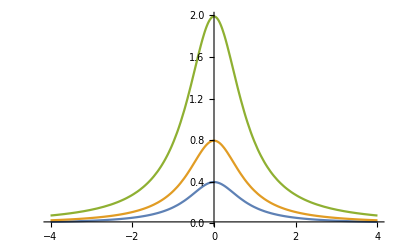

```mathematica
Plot[{Lorentzian[x,0,.8],Sum[Lorentzian[x,0,.8],{i,1,2}],Sum[Lorentzian[x,0,.8],{i,1,5}]},{x,-4,4},PlotRange->Full]
```

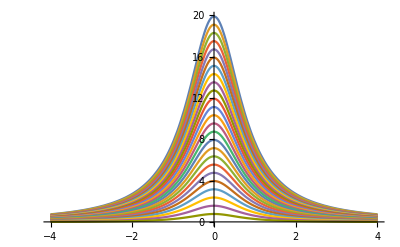

```mathematica
Plot[Evaluate[Table[Sum[Lorentzian[x,0,.8],{i,1,n}],{n,50,2,-2}]],{x,-4,4},PlotRange->Full]
```

```mathematica
Plot3D[Lorentzian[x,Sin[x0],.8],{x0,0,2Pi},{x,-4,4},PlotRange->Full,AxesLabel->{"x0","x","L(γ,x0,x)"},ViewPoint->{0, 0, 2}]
```

```mathematica
data=Table[Table[Sum[Lorentzian[x,Sin[Abs[n]*Pi/20],.5],{i,1,Abs[n]}],{n,-50,50,.5}],{x,-4,4,.1}];
```

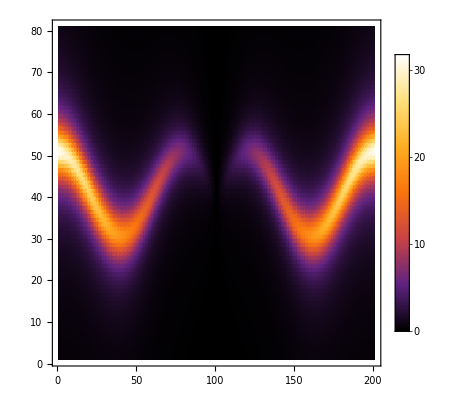

```mathematica
ListDensityPlot[data,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full]
```

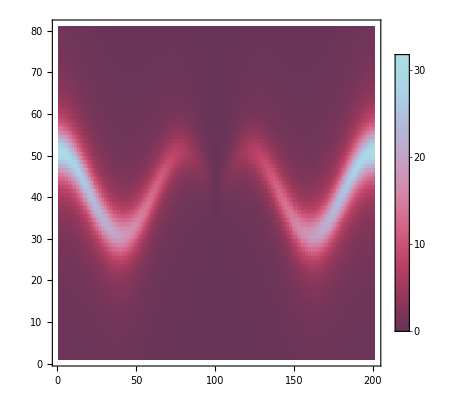

```mathematica
ListDensityPlot[data,ColorFunction->"CandyColors",PlotLegends->Automatic,PlotRange->Full]
```

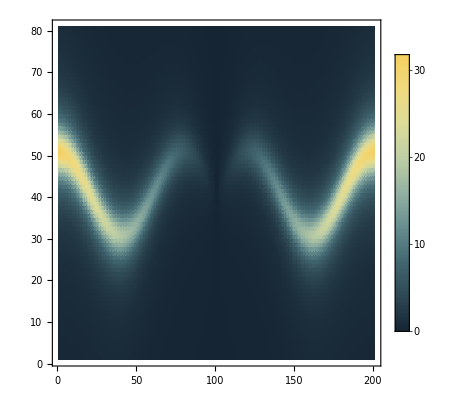

```mathematica
ListDensityPlot[data,ColorFunction->"StarryNightColors",PlotLegends->Automatic,PlotRange->Full]
```